```mathematica
(*----------------------------------------------------------------------------------------------------------------------------------------------*)
(*IMPORT LOGARITHMIC DERIVATIVES OF OPACITY, INTERPOLATE THEM AND FIND CHANGE IN OPACITY*)
(*Import logarithmic derivative of opacity with respect to individual elemental abundances and total metallicity*)
(*----------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
c=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/c.dat"];
n=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/n.dat"];
o=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/o.dat"];
ne=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/ne.dat"];
mg=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/mg.dat"];
si=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/si.dat"];
s=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/s.dat"];
fe=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/fe.dat"];
```

```mathematica
(*Interpolate data points for logarithmic derivatives of opacity*)
```

```mathematica
Fc=Interpolation[c];
Fn=Interpolation[n];
Fo=Interpolation[o];
Fne=Interpolation[ne];
Fmg=Interpolation[mg];
Fsi=Interpolation[si];
Fs=Interpolation[s];
Ffe=Interpolation[fe];
```

```mathematica
(*Plot logarithmic derivatives of opacity, reproduce Fig. 10 in 1312.3885 and blue curve in left panel of Fig. 2 of 0912.4696*)
```

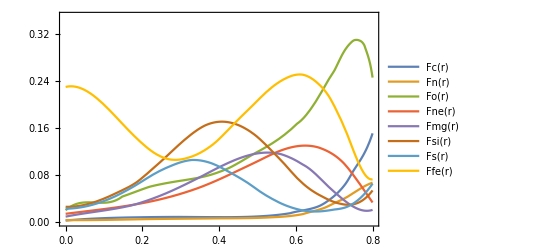

```mathematica
Quiet[Plot[{Fc[r],Fn[r],Fo[r],Fne[r],Fmg[r],Fsi[r],Fs[r],Ffe[r]},{r,0,0.8},PlotRange->{0,0.35},PlotLegends->"Expressions",Frame->True]]
```

```mathematica
(*Export logarithmic derivatives of opacity, plot using kziplotter*)
```

```mathematica
kzi=OpenWrite["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/kzi.dat",FormatType->OutputForm];
```

```mathematica
Quiet[Do[Write[kzi,0.01*i," ",SetPrecision[Fc[0.01*i],2]," ",SetPrecision[Fn[0.01*i],2]," ",SetPrecision[Fo[0.01*i],2]," ",SetPrecision[Fne[0.01*i],2]," ",SetPrecision[Fmg[0.01*i],2]," ",SetPrecision[Fsi[0.01*i],2]," ",SetPrecision[Fs[0.01*i],2]," ",SetPrecision[Ffe[0.01*i],2]," ",SetPrecision[Fz[0.01*i],2]],{i,1,80}]];
```

```mathematica
Close[kzi];
```

```mathematica
(*----------------------------------------------------------------------------------------------------------------------------------------------*)
(*IMPORT LOGARITHMIC DERIVATIVES OF SOUND SPEED AND INTERPOLATE THEM*)
(*Import logarithmic derivatives of sound speed with respect to individual elemental abundances*)
(*----------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
uc=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/uc.dat"];
un=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/un.dat"];
uo=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/uo.dat"];
une=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/une.dat"];
umg=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/umg.dat"];
usi=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/usi.dat"];
us=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/us.dat"];
ufe=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/ufe.dat"];
```

```mathematica
(*Interpolate data points for logarithmic derivatives of sound speed*)
```

```mathematica
Fuc=Interpolation[uc,InterpolationOrder->1];
Fun=Interpolation[un,InterpolationOrder->1];
Fuo=Interpolation[uo];
Fune=Interpolation[une];
Fumg=Interpolation[umg];
Fusi=Interpolation[usi];
Fus=Interpolation[us];
Fufe=Interpolation[ufe];
```

```mathematica
(*Plot logarithmic derivatives of sound speed, reproduce Fig. 4 in 1312.3885*)
```

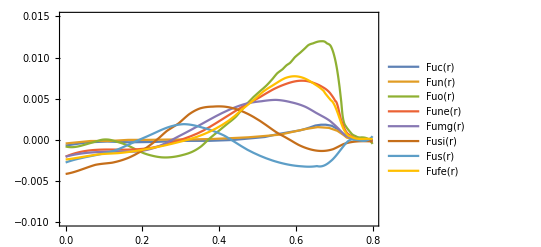

```mathematica
Quiet[Plot[{Fuc[r],Fun[r],Fuo[r],Fune[r],Fumg[r],Fusi[r],Fus[r],Fufe[r]},{r,0,0.8},PlotRange->{-0.01,0.015},PlotLegends->"Expressions",Frame->True]]
```

```mathematica
(*Export logarithmic derivatives of sound speed, plot using uziplotter*)
```

```mathematica
uzi=OpenWrite["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/uzi.dat",FormatType->OutputForm];
```

```mathematica
Quiet[Do[Write[uzi,0.01*i," ",SetPrecision[FortranForm[Fuc[0.01*i]],2]," ",SetPrecision[FortranForm[Fun[0.01*i]],2]," ",SetPrecision[Fuo[0.01*i],2]," ",SetPrecision[Fune[0.01*i],2]," ",SetPrecision[Fumg[0.01*i],2]," ",SetPrecision[Fusi[0.01*i],2]," ",SetPrecision[FortranForm[Fus[0.01*i]],2]," ",SetPrecision[Fufe[0.01*i],2]],{i,1,80}]];
```

```mathematica
Close[uzi];
```

```mathematica
(*----------------------------------------------------------------------------------------------------------------------------------------------*)
(*OLD AND NEW ABUNDANCES*)
(*Save old and new abundances, their errors, evaluate fraction change and errors*)
(*----------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*Save old abundances*)
```

```mathematica
ecold=8.43; decold=0.05;
enold=7.83; denold=0.05;
eoold=8.69; deoold=0.05;
eneold=7.93; deneold=0.10;
emgold=7.60;demgold=0.04;
esiold=7.51; desiold=0.03;
esold=7.12; desold=0.03;
efeold=7.50; defeold=0.04;
```

```mathematica
(*Save new abundances*)
```

```mathematica
ecnew=8.65; decnew=0.08;
ennew=7.97; dennew=0.08;
eonew=8.82; deonew=0.11;
enenew=7.79; denenew=0.08;
emgnew=7.85; demgnew=0.08;
esinew=7.82; desinew=0.08;
esnew=7.56; desnew=0.08;
efenew=7.73; defenew=0.08;
```

```mathematica
(*Evaluate fractional differences between abundances sets*)
```

```mathematica
dzc=10^(ecnew-ecold)-1;
dzn=10^(ennew-enold)-1;
dzo=10^(eonew-eoold)-1;
dzne=10^(enenew-eneold)-1;
dzmg=10^(emgnew-emgold)-1;
dzsi=10^(esinew-esiold)-1;
dzs=10^(esnew-esold)-1;
dzfe=10^(efenew-efeold)-1;
```

```mathematica
(*Evaluate or save errors on fractional differences*)
```

```mathematica
(*ddzc=2.303*Sqrt[decold^2+decnew^2]*dzc;
ddzn=2.303*Sqrt[denold^2+dennew^2]*dzn;
ddzo=2.303*Sqrt[deoold^2+deonew^2]*dzo;
ddzne=2.303*Sqrt[deneold^2+denenew^2]*dzne;
ddzmg=2.303*Sqrt[demgold^2+demgnew^2]*dzmg;
ddzsi=2.303*Sqrt[desiold^2+desinew^2]*dzsi;
ddzs=2.303*Sqrt[desold^2+desinew^2]*dzs;
ddzfe=2.303*Sqrt[defeold^2+defenew^2]*dzfe;*)
```

```mathematica
ddzc=0.15;
ddzn=0.08;
ddzo=0.10;
ddzne=0.08;
ddzmg=0.16;
ddzsi=0.21;
ddzs=0.35;
ddzfe=0.15;
```

```mathematica
(*----------------------------------------------------------------------------------------------------------------------------------------------*)
(*OPACITY, KERNELS, AND SOUND SPEED VARIATION*)
(*Import opacity and kernels for Y_s and R_b from Villante, including intrinsic opacity change, change in sound speed and calculate change in opacity*)
(*----------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
kappa=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/kappa.dat"];
kys=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/kys.dat"];
krb=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/krb.dat"];
ki=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/ki.dat"];
du=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/du.dat"];
```

```mathematica
(*Interpolate data points for opacity, opacity kernels and sound speed variation*)
```

```mathematica
Fkappa=Interpolation[kappa];
Fkys=Interpolation[kys];
Fkrb=Interpolation[krb,InterpolationOrder->1];
Fdu=Interpolation[du];
```

```mathematica
(*Plot Villante's change in opacity, right panel Fig. 10 of 1312.3885. We won't need it anyway*)
```

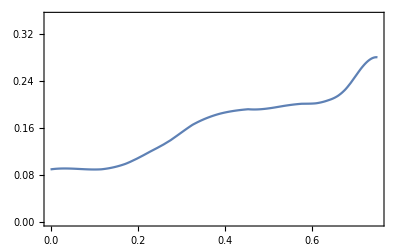

```mathematica
Quiet[Plot[Fkappa[r],{r,0,0.75},PlotRange->{0,0.35},Frame->True]]
```

```mathematica
(*Plot kernel for surface Helium, left panel Fig. 5 of 1006.3875*)
```

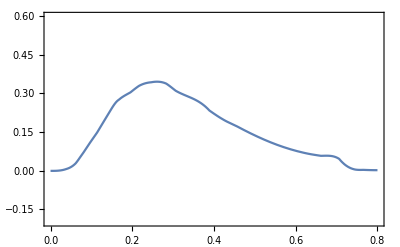

```mathematica
Plot[Fkys[r],{r,0,0.8},PlotRange->{-0.2,0.6},Frame->True]
```

```mathematica
(*Plot kernel for convective radius, right panel of Fig. 5 of 1006.3875*)
```

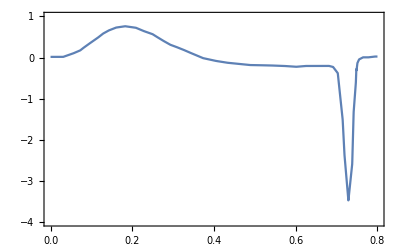

```mathematica
Plot[Fkrb[r],{r,0,0.8},PlotRange->{-4,1},Frame->True]
```

```mathematica
(*Plot change in sound speed, Fig. 1 black line in 1411.6626*)
```

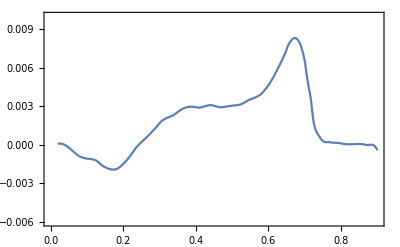

```mathematica
Plot[Fdu[r],{r,0.02,0.9},PlotRange->{-0.006,0.01},Frame->True]
```

```mathematica
(*Export surface Helium abundance and convective radius kernels and sound speed to plot in gnuplot*)
```

```mathematica
(*Plot using kyplotter*)
```

```mathematica
ky=OpenWrite["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/ky.dat",FormatType->OutputForm];
```

```mathematica
Quiet[Do[Write[ky,0.001*i," ",SetPrecision[FortranForm[Fkys[0.001*i]],2]],{i,1,800}]];
```

```mathematica
Close[ky];
```

```mathematica
(*Plot using krplotter*)
```

```mathematica
kr=OpenWrite["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/kr.dat",FormatType->OutputForm];
```

```mathematica
Quiet[Do[Write[kr,0.001*i," ",SetPrecision[FortranForm[Fkrb[0.001*i]],2]],{i,1,800}]];
```

```mathematica
Close[kr];
```

```mathematica
(*Plot using soundplotter*)
```

```mathematica
sound=OpenWrite["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/sound.dat",FormatType->OutputForm];
```

```mathematica
Quiet[Do[Write[sound,0.001*i," ",SetPrecision[FortranForm[Fdu[0.001*i]],2]],{i,1,800}]];
```

```mathematica
Close[sound];
```

```mathematica
(*Calculate opacity change due to metallicity change*)
```

```mathematica
dk[r_]:=Fc[r]*dzc+Fn[r]*dzn+Fo[r]*dzo+Fne[r]*dzne+Fmg[r]*dzmg+Fsi[r]*dzsi+Fs[r]*dzs+Ffe[r]*dzfe;
```

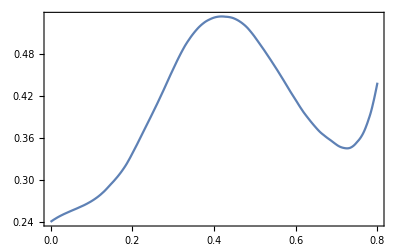

```mathematica
Quiet[Plot[dk[r],{r,0,0.8},PlotRange->All,Frame->True]]
```

```mathematica
(*Calculate error on opacity change due to metallicity change*)
```

```mathematica
ddk[r_]:=Sqrt[Fc[r]^2*ddzc^2+Fn[r]^2*ddzn^2+Fo[r]^2*ddzo^2+Fne[r]^2*ddzne^2+Fmg[r]^2*ddzmg^2+Fsi[r]^2*ddzsi^2+Fs[r]^2*ddzs^2+Ffe[r]^2*ddzfe^2];
```

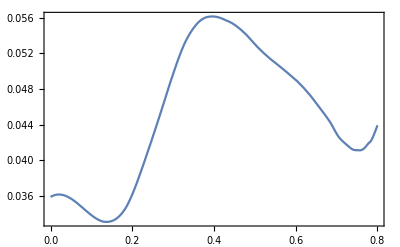

```mathematica
Quiet[Plot[ddk[r],{r,0,0.8},PlotRange->All,Frame->True]]
```

```mathematica
(*Export opacity change, plot using opacityplotter*)
```

```mathematica
opacity=OpenWrite["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/opacity.dat",FormatType->OutputForm];
```

```mathematica
Quiet[Do[Write[opacity,0.001*i," ",SetPrecision[FortranForm[dk[0.001*i]],3]," ",SetPrecision[FortranForm[dk[0.001*i]-ddk[0.001*i]],3]," ",SetPrecision[FortranForm[dk[0.001*i]+ddk[0.001*i]],3]," ",SetPrecision[FortranForm[dk[0.001*i]-2*ddk[0.001*i]],3]," ",SetPrecision[FortranForm[dk[0.001*i]+2*ddk[0.001*i]],3]],{i,1,800}]];
```

```mathematica
Close[opacity];
```

```mathematica
(*----------------------------------------------------------------------------------------------------------------------------------------------*)
(*REPONSE OF HELIOSEISMOLOGICAL OBSERVABLES*)
(*Calculate response of helioseismological observables, including modelling uncertainty*)
(*----------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*REPONSE OF SOUND SPEED*)
```

```mathematica
(*Response of sound speed using vSZ16 abundances*)
```

```mathematica
duz[r_]:=Fuc[r]*dzc+Fun[r]*dzn+Fuo[r]*dzo+Fune[r]*dzne+Fumg[r]*dzmg+Fusi[r]*dzsi+Fus[r]*dzs+Fufe[r]*dzfe;
```

```mathematica
(*Plot response of sound speed, after also including change in sound speed between AGSS09 and Sun*)
```

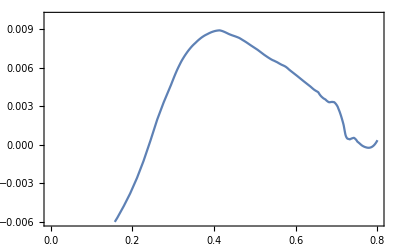

```mathematica
Quiet[Plot[duz[r],{r,0,0.8},PlotRange->{-0.006,0.01},Frame->True]]
```

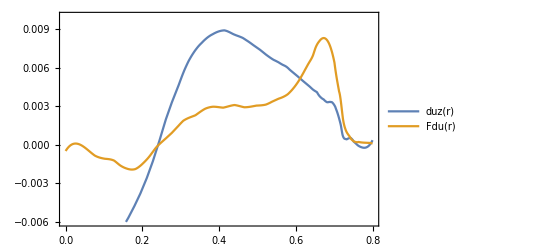

```mathematica
Quiet[Plot[{duz[r],Fdu[r]},{r,0,0.8},PlotRange->{-0.006,0.01},PlotLegends->"Expressions",Frame->True]]
```

```mathematica
(*Calculate error on vSZ16 sound speed profile*)
```

```mathematica
dduz[r_]:=Sqrt[Fuc[r]^2*ddzc^2+Fun[r]^2*ddzn^2+Fuo[r]^2*ddzo^2+Fune[r]^2*ddzne^2+Fumg[r]^2*ddzmg^2+Fusi[r]^2*ddzsi^2+Fus[r]^2*ddzs^2+Fufe[r]^2*ddzfe^2];
```

```mathematica
(*Export sound speed response with 1 sigma and 2 sigma errorbars, plot using soundzplotter*)
```

```mathematica
soundz=OpenWrite["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/soundz.dat",FormatType->OutputForm];
```

```mathematica
Quiet[Do[Write[soundz,0.001*i," ",SetPrecision[FortranForm[duz[0.001*i]],5]," ",SetPrecision[FortranForm[duz[0.001*i]-dduz[0.001*i]],5]," ",SetPrecision[FortranForm[duz[0.001*i]+dduz[0.001*i]],5]," ",SetPrecision[FortranForm[duz[0.001*i]-2*dduz[0.001*i]],5]," ",SetPrecision[FortranForm[duz[0.001*i]+2*dduz[0.001*i]],5]],{i,1,800}]];
```

```mathematica
Close[soundz];
```

```mathematica
(*Import model uncertainty*)
```

```mathematica
modunc=Import["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/modunc.dat"];
```

```mathematica
Fmodunc=Interpolation[modunc,InterpolationOrder->1];
```

```mathematica
(*Plot model uncertainty*)
```

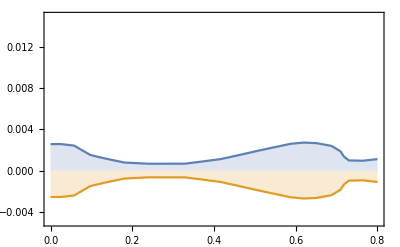

```mathematica
Quiet[Plot[{Fmodunc[r],-Fmodunc[r]},{r,0,0.8},PlotRange->{{0,0.8},{-0.005,0.015}},Filling->Axis,Frame->True]]
```

```mathematica
(*Export sound speed variation with 1 and 2 sigma correct uncertainty*)
```

```mathematica
soundnew=OpenWrite["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/soundnew.dat",FormatType->OutputForm];
```

```mathematica
Quiet[Do[Write[soundnew,0.001*i," ",SetPrecision[FortranForm[Fdu[0.001*i]-Fmodunc[0.001*i]],4]," ",SetPrecision[FortranForm[Fdu[0.001*i]+Fmodunc[0.001*i]],4]," ",SetPrecision[FortranForm[Fdu[0.001*i]-2*Fmodunc[0.001*i]],4]," ",SetPrecision[FortranForm[Fdu[0.001*i]+2*Fmodunc[0.001*i]],4]],{i,1,800}]];
```

```mathematica
Close[soundnew];
```

```mathematica
(*Calculate difference between vSZ16 sound speed variation and variation required to fix AGSS09*)
```

```mathematica
sounddiff[r_]:=duz[r]-Fdu[r];
```

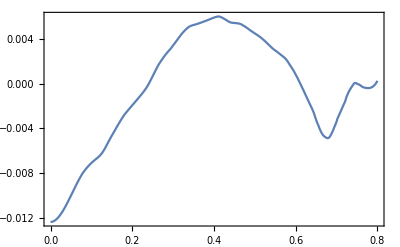

```mathematica
Quiet[Plot[sounddiff[r],{r,0,0.8},PlotRange->All,Frame->True]]
```

```mathematica
(*Calculate uncertainty on difference between vSZ16 sound speed variation and variation required to fix AGSS09*)
```

```mathematica
dsounddiff[r_]:=Sqrt[dduz[r]^2+Fmodunc[r]^2];
```

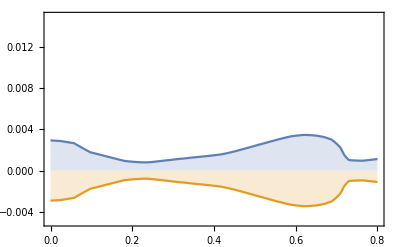

```mathematica
Quiet[Plot[{dsounddiff[r],-dsounddiff[r]},{r,0,0.8},PlotRange->{{0,0.8},{-0.005,0.015}},Filling->Axis,Frame->True]]
```

```mathematica
(*Export sound difference with 1 and 2 sigma correct uncertainties*)
```

```mathematica
sounddiffnew=OpenWrite["/home/sv/Dropbox/university/PhD/Stockholms Universitet/Projects/Revised DM abundances/Data and plots/Data/sounddiffnew.dat",FormatType->OutputForm];
```

```mathematica
Quiet[Do[Write[sounddiffnew,0.001*i," ",SetPrecision[FortranForm[sounddiff[0.001*i]],4]," ",SetPrecision[FortranForm[sounddiff[0.001*i]-dsounddiff[0.001*i]],4]," ",SetPrecision[FortranForm[sounddiff[0.001*i]+dsounddiff[0.001*i]],4]," ",SetPrecision[FortranForm[sounddiff[0.001*i]-2*dsounddiff[0.001*i]],4]," ",SetPrecision[FortranForm[sounddiff[0.001*i]+2*dsounddiff[0.001*i]],4]," ",0],{i,1,800}]];
```

```mathematica
Close[sounddiffnew];
```

```mathematica
(*Calculate average discrepancy between two profiles*)
```

```mathematica
NIntegrate[Sqrt[(sounddiff[r]/dsounddiff[r])^2],{r,0,0.73}]/0.73
```

2.50084

```mathematica
Abs[sounddiff[0.73]/dsounddiff[0.73]]
```

0.683124

```mathematica
Quiet[Abs[sounddiff[0.0]/dsounddiff[0.0]]]
```

4.21379

```mathematica
Quiet[Sum[Abs[sounddiff[0.01*i]/dsounddiff[0.01*i]],{i,0,73}]/73]
```

2.53286

```mathematica
(*RESPONSE OF SOUND SPEED FINISHED*)
```

```mathematica
(*RESPONSE OF SURFACE HELIUM ABUNDANCE*)
```

```mathematica
(*Save power-law exponents for surface Helium abundance*)
```

```mathematica
Ysc=-0.003; Ysn=0.001; Yso=0.025; Ysne=0.030; Ysmg=0.032; Yssi=0.063; Yss=0.043; Ysfe=0.086;
```

```mathematica
(*Calculate change in surface Helium abundance with power-law exponents*)
```

```mathematica
dyspl=Ysc*dzc+Ysn*dzn+Yso*dzo+Ysne*dzne+Ysmg*dzmg+Yssi*dzsi+Yss*dzs+Ysfe*dzfe
```

0.224874

```mathematica
(*Calculate change in surface Helium abundance integrating kernel*)
```

```mathematica
dys=NIntegrate[Fkys[r]*dk[r],{r,0,0.73}]
```

0.051712

```mathematica
(*Calculate uncertainty in change in surface Helium abundance using power-law exponents*)
```

```mathematica
ddys=Sqrt[Ysc^2*ddzc^2+Ysn^2*ddzn^2+Yso^2*ddzo^2+Ysne^2*ddzne^2+Ysmg^2*ddzmg^2+Yssi^2*ddzsi^2+Yss^2*ddzs^2+Ysfe^2*ddzfe^2]
```

0.0246248

```mathematica
(*Calculate new surface Helium abundance*)
```

```mathematica
ysnew=0.232+dys
```

0.283712

```mathematica
(*Calculate uncertainty on new surface Helium abundance*)
```

```mathematica
dysnew=Sqrt[0.003^2+ddys^2]
```

0.0248068

```mathematica
(*Save helioseismology value for surface Helium abundance*)
```

```mathematica
ysh=0.2485;dysh=0.0034;
```

```mathematica
(*Calculate discrepancy between vSZ16 and helioseismology*)
```

```mathematica
sigmays=(ysnew-ysh)/(Sqrt[dysnew^2+dysh^2])
```

1.4063

```mathematica
(*RESPONSE OF SURFACE HELIUM ABUNDANCE FINISHED*)
```

```mathematica
(*RESPONSE OF CONVECTIVE ZONE BOUNDARY*)
```

```mathematica
(*Save power-law exponents for convective zone boundary*)
```

```mathematica
Rbc=-0.005; Rbn=-0.003; Rbo=-0.027; Rbne=-0.011; Rbmg=-0.004; Rbsi=0.002; Rbs=0.004; Rbfe=-0.009;
```

```mathematica
(*Calculate change in convective zone boundary with power-law exponents*)
```

```mathematica
drbpl=Rbc*dzc+Rbn*dzn+Rbo*dzo+Rbne*dzne+Rbmg*dzmg+Rbsi*dzsi+Rbs*dzs+Rbfe*dzfe
```

-0.0111268

```mathematica
(*Calculate change in convective zone boundary integrating kernel*)
```

```mathematica
drb=NIntegrate[Fkrb[r]*dk[r],{r,0,0.8}]
```

-0.00842495

```mathematica
(*Calculate uncertainty in change in convective zone boundary using power-law exponents*)
```

```mathematica
ddrb=Sqrt[Rbc^2*ddzc^2+Rbn^2*ddzn^2+Rbo^2*ddzo^2+Rbne^2*ddzne^2+Rbmg^2*ddzmg^2+Rbsi^2*ddzsi^2+Rbs^2*ddzs^2+Rbfe^2*ddzfe^2]
```

0.00361289

```mathematica
(*Calculate new convective zone boundary*)
```

```mathematica
rbnew=0.723*(1+drbpl)
```

0.714955

```mathematica
(*Calculate uncertainty on new convective zone boundary*)
```

```mathematica
drbnew=0.002*(1+drbpl)
```

0.00197775

```mathematica
(*Save helioseismology value for convective zone boundary*)
```

```mathematica
rbh=0.713;drbh=0.001;
```

```mathematica
(*Calculate discrepancy between vSZ16 and helioseismology*)
```

```mathematica
sigmarb=(rbnew-rbh)/(Sqrt[drbnew^2+drbh^2])
```

0.882292

```mathematica
(*RESPONSE OF CONVECTIVE ZONE BOUNDARY FINISHED*)
```

```mathematica
(*RESPONSE OF NEUTRINO FLUXES*)
```

```mathematica
(*Save power-law exponents for Boron neutrinos flux*)
```

```mathematica
Bc=0.026;Bn=0.007;Bo=0.112;Bne=0.088;Bmg=0.089;Bsi=0.191;Bs=0.134;Bfe=0.501;
```

```mathematica
(*Calculate change in Boron neutrinos flux*)
```

```mathematica
dphib=Bc*dzc+Bn*dzn+Bo*dzo+Bne*dzne+Bmg*dzmg+Bsi*dzsi+Bs*dzs+Bfe*dzfe
```

0.887772

```mathematica
(*Calculate uncertainty in Boron neutrinos flux change*)
```

```mathematica
ddphib=Sqrt[Bc^2*ddzc^2+Bn^2*ddzn^2+Bo^2*ddzo^2+Bne^2*ddzne^2+Bmg^2*ddzmg^2+Bsi*ddzsi^2+Bs^2*ddzs^2+Bfe^2*ddzfe^2]
```

0.129087

```mathematica
(*Save power-law exponents for pp neutrinos flux*)
```

```mathematica
ppc=-0.005;ppn=-0.001;ppo=-0.004;ppne=-0.004;ppmg=-0.004;ppsi=-0.008;pps=-0.006;ppfe=-0.017;
```

```mathematica
(*Calculate change in pp neutrinos flux*)
```

```mathematica
dphipp=ppc*dzc+ppn*dzn+ppo*dzo+ppne*dzne+ppmg*dzmg+ppsi*dzsi+pps*dzs+ppfe*dzfe
```

-0.0378144

```mathematica
(*Calculate uncertainty in pp neutrinos flux change*)
```

```mathematica
ddphipp=Sqrt[ppc^2*ddzc^2+ppn^2*ddzn^2+ppo^2*ddzo^2+ppne^2*ddzne^2+ppmg^2*ddzmg^2+ppsi^2*ddzsi^2+pps^2*ddzs^2+ppfe^2*ddzfe^2]
```

0.00386986

```mathematica
(*Save power-law exponents for Berillium neutrinos flux change*)
```

```mathematica
Bec=0.004;Ben=0.002;Beo=0.052;Bene=0.046;Bemg=0.048;Besi=0.103;Bes=0.073;Befe=0.204;
```

```mathematica
(*Calculate change in Berillium neutrinos flux*)
```

```mathematica
dphiBe=Bec*dzc+Ben*dzn+Beo*dzo+Bene*dzne+Bemg*dzmg+Besi*dzsi+Bes*dzs+Befe*dzfe
```

0.424026

```mathematica
(*Calculate uncertainty in Berillium neutrinos flux change*)
```

```mathematica
ddphiBe=Sqrt[Bec^2*ddzc^2+Ben^2*ddzn^2+Beo^2*ddzo^2+Bene^2*ddzne^2+Bemg^2*ddzmg^2+Besi^2*ddzsi^2+Bes^2*ddzs^2+Befe^2*ddzfe^2]
```

0.0464432

```mathematica
(*Save power-law exponents for Nitrogen neutrinos flux change*)
```

```mathematica
Nc=0.874;Nn=0.147;No=0.057;Nne=0.042;Nmg=0.044;Nsi=0.102;Ns=0.072;Nfe=0.263;
```

```mathematica
(*Calculate change in Nitrogen neutrinos flux*)
```

```mathematica
dphiN=Nc*dzc+Nn*dzn+No*dzo+Nne*dzne+Nmg*dzmg+Nsi*dzsi+Ns*dzs+Nfe*dzfe
```

1.09116

```mathematica
(*Calculate uncertainty in Nitrogen neutrinos flux change*)
```

```mathematica
ddphiN=Sqrt[Nc^2*ddzc^2+Nn^2*ddzn^2+No^2*ddzo^2+Nne^2*ddzne^2+Nmg^2*ddzmg^2+Nsi^2*ddzsi^2+Ns^2*ddzs^2+Nfe^2*ddzfe^2]
```

0.141665

```mathematica
(*Save power-law exponents for Oxygen neutrinos flux change*)
```

```mathematica
Oc=0.827;Onnew=0.206;Oo=0.084;One=0.062;Omg=0.065;Osi=0.145;Os=0.102;Ofe=0.382;
```

```mathematica
(*Calculate change in Oxygen neutrinos flux*)
```

```mathematica
dphiO=Oc*dzc+Onnew*dzn+Oo*dzo+One*dzne+Omg*dzmg+Osi*dzsi+Os*dzs+Ofe*dzfe
```

1.28337

```mathematica
(*Calculate uncertainty in Oxygen neutrinos flux change*)
```

```mathematica
ddphiO=Sqrt[Oc^2*ddzc^2+Onnew^2*ddzn^2+Oo^2*ddzo^2+One^2*ddzne^2+Omg^2*ddzmg^2+Osi^2*ddzsi^2+Os^2*ddzs^2+Ofe^2*ddzfe^2]
```

0.146111

```mathematica
(*RESPONSE OF NEUTRINO FLUXES FINISHED*)
```